```mathematica
ClearAll["Global`*"]
t0 =.;te=.; w=.;tf=.;
x0=.; xe=.; v0=.; ve=.;
c1=.;c2=.;c3=.;c4=.;

J[a_]=0.5*a^2 ;

lamda1[t_] := c1;
lamda2[t_] := -c1*t+c2;
a[t_] := c1*t-c2;
v[t_] := 1/2*c1*t^2 - c2*t + c3;
x[t_] := 1/6*c1*t^3 - 1/2*c2*t^2 + c3*t + c4; 

c = Solve[{v[t0] == v0, v[te] == ve, x[t0] == x0, x[te] == xe}, {c1,c2,c3,c4}];
c1 = c1/.c[[1]];
c2 = c2/.c[[1]];
c3 = c3/.c[[1]];
c4 = c4/.c[[1]];
H[t_]=0.5*a[t]^2+lamda1[t]*v[t]+lamda2[t]*a[t] + 0.5*w;

(* Scenario 2.1 *)
w= 0.1;
t0=15;
x0=200;xe=250;
v0=.;ve = 11;

tf=Solve[H[te]==0 && te>0 && v0≥0,te,Reals];
Normal[tf]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{te→Root[-3.91838×10^6-279000. v0-9000. v0^2+(263700.+25200. v0+1200. v0^2) #1+(-3490.-440. v0-40. v0^2) #1^2-60. #1^3+#1^4&,2]},{te→Root[-3.91838×10^6-279000. v0-9000. v0^2+(263700.+25200. v0+1200. v0^2) #1+(-3490.-440. v0-40. v0^2) #1^2-60. #1^3+#1^4&,3]},{te→Root[-3.91838×10^6-279000. v0-9000. v0^2+(263700.+25200. v0+1200. v0^2) #1+(-3490.-440. v0-40. v0^2) #1^2-60. #1^3+#1^4&,4]}}

```mathematica
Red light
```

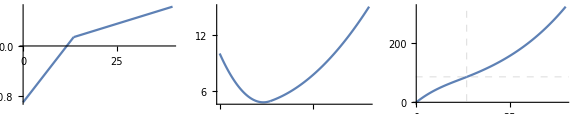

The cost for free time ({39.9164} s) case is {3.93755}

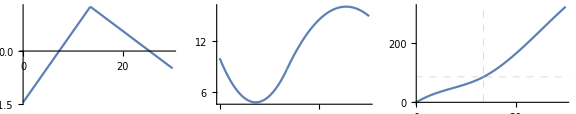

The cost for fixed time ({30.} s) case is {7.64108}

```mathematica
ClearAll["Global`*"]
t0 =.;t1=.;te=.; w=.; tf=.;tefixed=.;
x0=.;xred=.; xe=.; v0=.; ve=.;
c1=.;c2=.;c3=.;c4=.;c5=.;

H[t_]=0.5*a1[t]^2+lamda1[t]*v1[t]+lamda2[t]*a1[t] + 0.5*w^2;

lamda1[t_] := c1;
lamda2[t_] := -c1*t+c2;
a1[t_] := c1*t-c2;
a2[t_] := c1*t-c2 + c5*(t-t1);
v1[t_] := (1/2)*c1*t^2 - c2*t + c3;
v2[t_] := (1/2)*c1*t^2 - c2*t + c3 + 0.5*c5*(t-t1)^2;
x1[t_] := (1/6)*c1*t^3 - (1/2)*c2*t^2 + c3*t + c4; 
x2[t_] := (1/6)*c1*t^3 - (1/2)*c2*t^2 + c3*t + c4 + (1/6)*c5*(t-t1)^3; 

cc = Solve[{v1[t0]==v0, v2[te]==ve, x1[t0]==x0, x2[t1]==xred, x2[te]==xe, x1[t1]==xred}, {c1,c2,c3,c4,c5}];

c1 = c1/.cc[[1]];
c2 = c2/.cc[[1]];
c3 = c3/.cc[[1]];
c4 = c4/.cc[[1]];
c5 = c5/.cc[[1]];

(*Initial and Terinal Conditions*)
t0=0.0;t1=13.5; w=0.1;
v0=10.0; ve=15.0; x0 = 0.0;xred=85.0; xe = 320.0;
tefixed = 30.0;

(*Free Time*)
Hte=0.5*a2[te]^2+lamda1[te]*v2[te]+lamda2[te]*a2[te] + 0.5*w^2;
tf=NSolve[{Hte==0.0, te>0, te>t1},te,Reals];
te=te/.tf[[1]];

(*Cost and Plots for free time case*)
Jfree[t_]=Integrate[0.5*a1[t]^2,{t,t0,t1}]+Integrate[0.5*a2[t]^2,{t,t1,te}]+ 0.5*w^2*te;
GraphicsRow[{Show[{Plot[a1[t],{t,t0,t1}],Plot[a2[t],{t,t1,te}]},PlotRange->All,AxesOrigin->{0,0}],Show[{Plot[v1[t],{t,t0,t1}],Plot[v2[t],{t,t1,te}]},PlotRange->All,AxesOrigin->{0,0}],Show[{Plot[x1[t],{t,t0,t1}],Plot[x2[t],{t,t1,te}]},PlotRange->All,AxesOrigin->{0,0},
 GridLines-> {{{t1,Dashed}},{{xred,Dashed}}}]}, ImageSize->Large]

StringForm["The cost for free time (`2` s) case is `1`", {Jfree[t]}, {te}]

(*Cost and Plots for fixed time case*)
te = tefixed;
Jfixed[t_]=Integrate[0.5*a1[t]^2,{t,t0,t1}]+Integrate[0.5*a2[t]^2,{t,t1,te}]+ 0.5*w^2*tefixed;
GraphicsRow[{Show[{Plot[a1[t],{t,t0,t1}],Plot[a2[t],{t,t1,tefixed}]},PlotRange->All,AxesOrigin->{0,0}],Show[{Plot[v1[t],{t,t0,t1}],Plot[v2[t],{t,t1,tefixed}]},PlotRange->All,AxesOrigin->{0,0}],Show[{Plot[x1[t],{t,t0,t1}],Plot[x2[t],{t,t1,tefixed}]},PlotRange->All,AxesOrigin->{0,0}, GridLines-> {{{t1,Dashed}},{{xred,Dashed}}} ]},ImageSize->Large]

StringForm["The cost for fixed time (`2` s) case is `1`",{Jfixed[t]}, {tefixed}]
```